```mathematica
F1=√((Fz^2+Fy^2)1/9 f^2+Fx^2(1-4/3 f+4/9 f^2))
F2=√((Fx^2+Fz^2)1/9 f^2+Fy^2(1-4/3 f+4/9 f^2))
F3=√((Fx^2+Fy^2)1/9 f^2+Fz^2(1-4/3 f+4/9 f^2))
```

√((1-(4 f)/3+(4 f^2)/9) Fx^2+1/9 f^2 (Fy^2+Fz^2))

√((1-(4 f)/3+(4 f^2)/9) Fy^2+1/9 f^2 (Fx^2+Fz^2))

√(1/9 f^2 (Fx^2+Fy^2)+(1-(4 f)/3+(4 f^2)/9) Fz^2)

```mathematica
CForm[(F1+F2+F3)/E0]
```

(Sqrt((Power(f,2)*(Power(Fx,2) + Power(Fy,2)))/9. + (1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fz,2)) + Sqrt((1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fy,2) + (Power(f,2)*(Power(Fx,2) + Power(Fz,2)))/9.) + 
     Sqrt((1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fx,2) + (Power(f,2)*(Power(Fy,2) + Power(Fz,2)))/9.))/E0

```mathematica
CForm[%]
```

0 == -E0 + Sqrt((Power(f,2)*(Power(Fx,2) + Power(Fy,2)))/9. + (1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fz,2)) + Sqrt((1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fy,2) + (Power(f,2)*(Power(Fx,2) + Power(Fz,2)))/9.) + 
    Sqrt((1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fx,2) + (Power(f,2)*(Power(Fy,2) + Power(Fz,2)))/9.)

```mathematica
e1=F1+F2+F3-1
```

-1+√(1/9 f^2 (Fx^2+Fy^2)+(1-(4 f)/3+(4 f^2)/9) Fz^2)+√((1-(4 f)/3+(4 f^2)/9) Fy^2+1/9 f^2 (Fx^2+Fz^2))+√((1-(4 f)/3+(4 f^2)/9) Fx^2+1/9 f^2 (Fy^2+Fz^2))

```mathematica
sf1=Series[e1,{f,1,4}]
```

(-1+√(Fx^2+Fy^2+Fz^2))+(3 (Fx^2 Fy^2+Fx^2 Fz^2+Fy^2 Fz^2) (f-1)^2)/((Fx^2+Fy^2+Fz^2)^(3/2))+(3 (Fx^4 Fy^2+Fx^2 Fy^4+Fx^4 Fz^2-6 Fx^2 Fy^2 Fz^2+Fy^4 Fz^2+Fx^2 Fz^4+Fy^2 Fz^4) (f-1)^3)/(2 (Fx^2+Fy^2+Fz^2)^(5/2))+(3 (10 Fx^6 Fy^2-25 Fx^4 Fy^4+10 Fx^2 Fy^6+10 Fx^6 Fz^2-13 Fx^4 Fy^2 Fz^2-13 Fx^2 Fy^4 Fz^2+10 Fy^6 Fz^2-25 Fx^4 Fz^4-13 Fx^2 Fy^2 Fz^4-25 Fy^4 Fz^4+10 Fx^2 Fz^6+10 Fy^2 Fz^6) (f-1)^4)/(4 (Fx^2+Fy^2+Fz^2)^(7/2))+O[f-1]^5

```mathematica
sf1
```

(-1+√(Fx^2+Fy^2+Fz^2))+(3 (Fx^2 Fy^2+Fx^2 Fz^2+Fy^2 Fz^2) (f-1)^2)/((Fx^2+Fy^2+Fz^2)^(3/2))+(3 (Fx^4 Fy^2+Fx^2 Fy^4+Fx^4 Fz^2-6 Fx^2 Fy^2 Fz^2+Fy^4 Fz^2+Fx^2 Fz^4+Fy^2 Fz^4) (f-1)^3)/(2 (Fx^2+Fy^2+Fz^2)^(5/2))+(3 (10 Fx^6 Fy^2-25 Fx^4 Fy^4+10 Fx^2 Fy^6+10 Fx^6 Fz^2-13 Fx^4 Fy^2 Fz^2-13 Fx^2 Fy^4 Fz^2+10 Fy^6 Fz^2-25 Fx^4 Fz^4-13 Fx^2 Fy^2 Fz^4-25 Fy^4 Fz^4+10 Fx^2 Fz^6+10 Fy^2 Fz^6) (f-1)^4)/(4 (Fx^2+Fy^2+Fz^2)^(7/2))+O[f-1]^5

```mathematica
Plot[{Evaluate[sf[[1,1,2]]/.{Fx->1/(√3),Fy->1/(√3),Fz->1/(√3)}],Evaluate[sf1/.{Fx->1/(√3),Fy->1/(√3),Fz->1/(√3)}]},{E0,0,3}]
```

-Graphics-

```mathematica
CForm[%]
```

0 == -E0 + Sqrt((Power(f,2)*(Power(Fx,2) + Power(Fy,2)))/9. + (1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fz,2)) + Sqrt((1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fy,2) + (Power(f,2)*(Power(Fx,2) + Power(Fz,2)))/9.) + 
    Sqrt((1 - (4*f)/3. + (4*Power(f,2))/9.)*Power(Fx,2) + (Power(f,2)*(Power(Fy,2) + Power(Fz,2)))/9.)

```mathematica
sf=Solve[(E0==F1+F2+F3)/.{Fx->1/(√3),Fy->1/(√3),Fz->1/(√3)},f]
```

{{f→1/2 (2-√2 √(-1+E0^2))},{f→1/2 (2+√2 √(-1+E0^2))}}

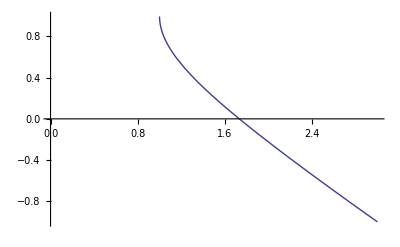

```mathematica
Plot[Evaluate[sf[[1,1,2]]/.{Fx->1/(√3),Fy->1/(√3),Fz->1/(√3)}],{E0,0,3}]
```

```mathematica
sf=Solve[F1 E0==F1^2+F2^2+F3^2,f]
```

{{f→1-1/2 √(«5»+«1»)-1/2 √(8-(-4 E0^2 Fx^2+28 Fx^4-E0^2 Fy^2+«4»+56 Fx^2 Fz^2+56 Fy^2 Fz^2+28 Fz^4)/(4 (Fx^2+Fy^2+Fz^2)^2)-(«1»)/(12 (Fx^4+«4»+«1»))-(«1»-«1»«1»«1»)/(«1»)-(«1»)^(1/3)/(12 2^(1/3) («1»)^2)-(64-(24 (E0^2 Fx^2-2 Fx^4-4 Fx^2 Fy^2-2 Fy^4-4 Fx^2 Fz^2-4 Fy^2 Fz^2-2 Fz^4))/((Fx^2+Fy^2+Fz^2)^2)-(4 (-4 E0^2 Fx^2+28 Fx^4-E0^2 Fy^2+56 Fx^2 Fy^2+28 Fy^4-E0^2 Fz^2+56 Fx^2 Fz^2+56 Fy^2 Fz^2+28 Fz^4))/((Fx^2+Fy^2+Fz^2)^2))/(4 √(4-(-4 E0^2 Fx^2+28 Fx^4-E0^2 Fy^2+56 Fx^2 Fy^2+28 Fy^4-E0^2 Fz^2+56 Fx^2 Fz^2+56 Fy^2 Fz^2+28 Fz^4)/(4 (Fx^2+Fy^2+Fz^2)^2)+(-4 E0^2 Fx^2+«9»+28 («2»)^4)/(12 (Fx^4+«4»+Fz^4))+(576 («1») (Fx^4+2 Fx^2 Fy^2+Fy^4+2 Fx^2 Fz^2+2 Fy^2 Fz^2+Fz^4)-«1»+(«1»)^2)/(6 2^(2/3) (Fx^2+Fy^2+Fz^2)^2 («1»)^(1/3))+(«6»+√(«1»))^(1/3)/(12 2^(1/3) (Fx^2+Fy^2+Fz^2)^2))))},«3»}

```mathematica
Plot[Evaluate[sf[[1,1,2]]/.{Fx->1/(√3),Fy->1/(√3),Fz->1/(√3)}],{E0,0,3}]
```

-Graphics-

```mathematica
CForm[sf[[2,1,2]]]
```

(Power(E0,2)*Power(Fx,2) - Power(Fx,4) + Power(E0,2)*Power(Fy,2) + 
     2*Power(Fx,2)*Power(Fy,2) - Power(Fy,4) + 
     Sqrt(Power(E0,6)*Power(Fx,2) - 2*Power(E0,4)*Power(Fx,4) + 
       Power(E0,2)*Power(Fx,6) + Power(E0,6)*Power(Fy,2) - 
       Power(E0,2)*Power(Fx,4)*Power(Fy,2) - 
       2*Power(E0,4)*Power(Fy,4) - 
       Power(E0,2)*Power(Fx,2)*Power(Fy,4) + Power(E0,2)*Power(Fy,6)
       ))/(Power(E0,2)*Power(Fx,2) - Power(Fx,4) + 
     Power(E0,2)*Power(Fy,2) + 2*Power(Fx,2)*Power(Fy,2) - 
     Power(Fy,4))